```mathematica
Quit
```

# EDA

## Database

#### Information about variables

Notes for Football Data

All data is in csv format, ready for use within standard spreadsheet applications. Please note that some abbreviations are no longer in use (in particular odds from specific bookmakers no longer used) and refer to data collected in earlier seasons. For a current list of what bookmakers are included in the dataset please visit http://www.football-data.co.uk/matches.php

Key to results data:

Div = League Division
Date = Match Date (dd/mm/yy)
Time = Time of match kick off
HomeTeam = Home Team
AwayTeam = Away Team
FTHG and HG = Full Time Home Team Goals
FTAG and AG = Full Time Away Team Goals
FTR and Res = Full Time Result (H=Home Win, D=Draw, A=Away Win)
HTHG = Half Time Home Team Goals
HTAG = Half Time Away Team Goals
HTR = Half Time Result (H=Home Win, D=Draw, A=Away Win)

Match Statistics (where available)
Attendance = Crowd Attendance
Referee = Match Referee
HS = Home Team Shots
AS = Away Team Shots
HST = Home Team Shots on Target
AST = Away Team Shots on Target
HHW = Home Team Hit Woodwork
AHW = Away Team Hit Woodwork
HC = Home Team Corners
AC = Away Team Corners
HF = Home Team Fouls Committed
AF = Away Team Fouls Committed
HFKC = Home Team Free Kicks Conceded
AFKC = Away Team Free Kicks Conceded
HO = Home Team Offsides
AO = Away Team Offsides
HY = Home Team Yellow Cards
AY = Away Team Yellow Cards
HR = Home Team Red Cards
AR = Away Team Red Cards
HBP = Home Team Bookings Points (10 = yellow, 25 = red)
ABP = Away Team Bookings Points (10 = yellow, 25 = red)

Note that Free Kicks Conceeded includes fouls, offsides and any other offense commmitted and will always be equal to or higher than the number of fouls. Fouls make up the vast majority of Free Kicks Conceded. Free Kicks Conceded are shown when specific data on Fouls are not available (France 2nd, Belgium 1st and Greece 1st divisions).

Note also that English and Scottish yellow cards do not include the initial yellow card when a second is shown to a player converting it into a red, but this is included as a yellow (plus red) for European games.

Key to 1X2 (match) betting odds data:

B365H = Bet365 home win odds
B365D = Bet365 draw odds
B365A = Bet365 away win odds
BSH = Blue Square home win odds
BSD = Blue Square draw odds
BSA = Blue Square away win odds
BWH = Bet&Win home win odds
BWD = Bet&Win draw odds
BWA = Bet&Win away win odds
GBH = Gamebookers home win odds
GBD = Gamebookers draw odds
GBA = Gamebookers away win odds
IWH = Interwetten home win odds
IWD = Interwetten draw odds
IWA = Interwetten away win odds
LBH = Ladbrokes home win odds
LBD = Ladbrokes draw odds
LBA = Ladbrokes away win odds
PSH and PH = Pinnacle home win odds
PSD and PD = Pinnacle draw odds
PSA and PA = Pinnacle away win odds
SOH = Sporting Odds home win odds
SOD = Sporting Odds draw odds
SOA = Sporting Odds away win odds
SBH = Sportingbet home win odds
SBD = Sportingbet draw odds
SBA = Sportingbet away win odds
SJH = Stan James home win odds
SJD = Stan James draw odds
SJA = Stan James away win odds
SYH = Stanleybet home win odds
SYD = Stanleybet draw odds
SYA = Stanleybet away win odds
VCH = VC Bet home win odds
VCD = VC Bet draw odds
VCA = VC Bet away win odds
WHH = William Hill home win odds
WHD = William Hill draw odds
WHA = William Hill away win odds

Bb1X2 = Number of BetBrain bookmakers used to calculate match odds averages and maximums
BbMxH = Betbrain maximum home win odds
BbAvH = Betbrain average home win odds
BbMxD = Betbrain maximum draw odds
BbAvD = Betbrain average draw win odds
BbMxA = Betbrain maximum away win odds
BbAvA = Betbrain average away win odds

MaxH = Market maximum home win odds
MaxD = Market maximum draw win odds
MaxA = Market maximum away win odds
AvgH = Market average home win odds
AvgD = Market average draw win odds
AvgA = Market average away win odds

Key to total goals betting odds:

BbOU = Number of BetBrain bookmakers used to calculate over/under 2.5 goals (total goals) averages and maximums
BbMx>2.5 = Betbrain maximum over 2.5 goals
BbAv>2.5 = Betbrain average over 2.5 goals
BbMx<2.5 = Betbrain maximum under 2.5 goals
BbAv<2.5 = Betbrain average under 2.5 goals

GB>2.5 = Gamebookers over 2.5 goals
GB<2.5 = Gamebookers under 2.5 goals
B365>2.5 = Bet365 over 2.5 goals
B365<2.5 = Bet365 under 2.5 goals
P>2.5 = Pinnacle over 2.5 goals
P<2.5 = Pinnacle under 2.5 goals
Max>2.5 = Market maximum over 2.5 goals
Max<2.5 = Market maximum under 2.5 goals
Avg>2.5 = Market average over 2.5 goals
Avg<2.5 = Market average under 2.5 goals

Key to Asian handicap betting odds:

BbAH = Number of BetBrain bookmakers used to Asian handicap averages and maximums
BbAHh = Betbrain size of handicap (home team)
AHh = Market size of handicap (home team) (since 2019/2020)
BbMxAHH = Betbrain maximum Asian handicap home team odds
BbAvAHH = Betbrain average Asian handicap home team odds
BbMxAHA = Betbrain maximum Asian handicap away team odds
BbAvAHA = Betbrain average Asian handicap away team odds

GBAHH = Gamebookers Asian handicap home team odds
GBAHA = Gamebookers Asian handicap away team odds
GBAH = Gamebookers size of handicap (home team)
LBAHH = Ladbrokes Asian handicap home team odds
LBAHA = Ladbrokes Asian handicap away team odds
LBAH = Ladbrokes size of handicap (home team)
B365AHH = Bet365 Asian handicap home team odds
B365AHA = Bet365 Asian handicap away team odds
B365AH = Bet365 size of handicap (home team)
PAHH = Pinnacle Asian handicap home team odds
PAHA = Pinnacle Asian handicap away team odds
MaxAHH = Market maximum Asian handicap home team odds
MaxAHA = Market maximum Asian handicap away team odds	
AvgAHH = Market average Asian handicap home team odds
AvgAHA = Market average Asian handicap away team odds


Closing odds (last odds before match starts)
As above but with an additional “C” character following the bookmaker abbreviation/Max/Avg
Football-Data would like to acknowledge the following sources which have been utilised in the compilation of Football-Data’s results and odds files.
Current results (full time, half time)
XScores - http://www.xscores .com
Match statistics
BBC, ESPN Soccer, Bundesliga.de, Gazzetta.it and Football.fr
Bookmakers betting odds
Individual bookmakers
Betting odds for weekend games are collected Friday afternoons, and on Tuesday afternoons for midweek games.
Additional match statistics (corners, shots, bookings, referee etc.) for the 2000/01 and 2001/02 seasons for the English, Scottish and German leagues were provided by Sports.com (now under new ownership and no longer available).

#### Database construction

```mathematica
chooseLeague = "L";
(*Importación de los datos*)
If[chooseLeague=="La Liga",
	df2425 = Import["https://www.football-data.co.uk/mmz4281/2425/SP1.csv", "CSV"];
	df2324 = Import["https://www.football-data.co.uk/mmz4281/2324/SP1.csv", "CSV"];
	df2223 = Import["https://www.football-data.co.uk/mmz4281/2223/SP1.csv", "CSV"];
	df2122 = Import["https://www.football-data.co.uk/mmz4281/2122/SP1.csv", "CSV"];
	df2021 = Import["https://www.football-data.co.uk/mmz4281/2021/SP1.csv", "CSV"];
	df1920 = Import["https://www.football-data.co.uk/mmz4281/1920/SP1.csv", "CSV"];
	,
	(*Importación de los datos*)
	df2425=Import["https://www.football-data.co.uk/mmz4281/2425/E0.csv","CSV"];
	df2324=Import["https://www.football-data.co.uk/mmz4281/2324/E0.csv","CSV"];
	df2223=Import["https://www.football-data.co.uk/mmz4281/2223/E0.csv","CSV"];
	df2122=Import["https://www.football-data.co.uk/mmz4281/2122/E0.csv","CSV"];
	df2021=Import["https://www.football-data.co.uk/mmz4281/2021/E0.csv","CSV"];
	df1920=Import["https://www.football-data.co.uk/mmz4281/1920/E0.csv","CSV"];
	];
	
(* Corroborar que todas las variables sean comunes entre bases de datos *)
(*
Complement[df2425[[1]], df2324[[1]]];
Complement[df2324[[1]], df2425[[1]]];
*)

(* Eliminar variables que no sean comunes entre bases de datos *)
indices2425 = Reverse[Sort[Flatten[Position[df2425[[1]], #] & /@ Complement[df2425[[1]], df2324[[1]]]]]];
indices2324 = Reverse[Sort[Flatten[Position[df2324[[1]], #] & /@ Complement[df2324[[1]], df2425[[1]]]]]];
indices2223 = Reverse[Sort[Flatten[Position[df2223[[1]], #] & /@ Complement[df2223[[1]], df2425[[1]]]]]];
indices2122 = Reverse[Sort[Flatten[Position[df2223[[1]], #] & /@ Complement[df2122[[1]], df2425[[1]]]]]];
indices2021 = Reverse[Sort[Flatten[Position[df2021[[1]], #] & /@ Complement[df2021[[1]], df2425[[1]]]]]];
indices1920 = Reverse[Sort[Flatten[Position[df2021[[1]], #] & /@ Complement[df1920[[1]], df2425[[1]]]]]];

df2425 = df2425[[All, Complement[Range[Length[df2425[[1]]]], indices2425]]];
df2324 = df2324[[All, Complement[Range[Length[df2324[[1]]]], indices2324]]];
df2223 = df2223[[All, Complement[Range[Length[df2223[[1]]]], indices2223]]];
df2122 = df2122[[All, Complement[Range[Length[df2122[[1]]]], indices2122]]];
df2021 = df2021[[All, Complement[Range[Length[df2021[[1]]]], indices2021]]];
df1920 = df1920[[All, Complement[Range[Length[df1920[[1]]]], indices1920]]];

(*Obtener los nombres de las columnas de uno de los dataframes*)
columnNames=First[df2425];

(*Eliminar la primera fila de cada dataframe (los encabezados) y añadir la columna Season*)
df2425=Append[#,"2425"]&/@Rest[df2425];
df2324=Append[#,"2324"]&/@Rest[df2324];
df2223=Append[#,"2223"]&/@Rest[df2223];
df2122=Append[#,"2122"]&/@Rest[df2122];
df2021=Append[#,"2021"]&/@Rest[df2021];
df1920=Append[#,"1920"]&/@Rest[df1920];

(*Unir los dataframes*)
dfList=Join[{Append[columnNames,"Season"]},df2425,df2324,df2223,df2122,df2021,df1920];
```

```mathematica
Export["C:/Users/geral/OneDrive - Universidad del Pacífico/Trabajos/CMA/data_ligainglesa2.csv",dfList];
```

#### Importing data

```mathematica
(*
If[chooseLeague=="La Liga",
	dfList = Import["C:/Users/geral/OneDrive - Universidad del Pacífico/Trabajos/CMA/data_ligaespana.csv"],
	dfList = Import["C:/Users/geral/OneDrive - Universidad del Pacífico/Trabajos/CMA/data_ligainglesa2.csv"]
	];
*)
dfList = Import["C:/Users/geral/OneDrive - Universidad del Pacífico/Trabajos/CMA/data_ligainglesa2.csv"];
dfAssociation=AssociationThread[dfList[[1]]->#]&/@Rest[dfList];
dfDataSet=Dataset[dfAssociation];
dfDataSet=dfDataSet[All,Append[#,"Total"->(#FTHG+#FTAG)]&];
dfDataSet=dfDataSet[All,Append[#,"DifferenceGoals"->(Abs[#FTHG-#FTAG])]&];
```

#### Importing database

```mathematica
dataList = Import["C:/Users/geral/OneDrive - Universidad del Pacífico/Trabajos/CMA/data_ligainglesa2.csv"];
dateList = DateObject[{ToExpression[StringTake[#, {7, 10}]], 
                                ToExpression[StringTake[#, {4, 5}]], 
                                ToExpression[StringTake[#, {1, 2}]]}] & /@ 
                                (Rest[dataList[[All,2]]]);
dataAssociation=AssociationThread[dataList[[1]]->#]&/@Rest[dataList];
dataAssociation=MapThread[Append[#1, "DateConverted" -> #2] &, {dataAssociation, dateList}];
(* Working with dataset *)
dataDS = Dataset[dataAssociation];
dataDS = dataDS[All, Append[#, "MatchTeams" -> {#HomeTeam, #AwayTeam}] &];
dataDS = dataDS[All, Append[#, "Total" -> (#FTHG + #FTAG)] &];
dataDS = dataDS[All, Append[#, "DifferenceGoals" -> Abs[#FTHG - #FTAG]] &];
dataDS = SortBy[dataDS,#DateConverted &];
(* Working with Tabular *)
(*dataTabular = Tabular[dataAssociation];*)
```

```mathematica
(* Inicializar parámetros ELO *)
initialElo = 1500;
kFactor = 10;
(* Función para calcular la puntuación esperada *)
expectedScore[ratingA_, ratingB_] := 1/(1 + 10^((ratingB - ratingA)/400));
(* Función para actualizar la calificación ELO *)
updateElo[currentRating_, expected_, actual_] := currentRating + kFactor * (actual - expected);
(* Inicializar diccionario de calificaciones ELO *)
eloRatings = <||>;
(* Procesar cada partido para actualizar las calificaciones ELO *)
dataDS[All, 
  Function[match, 
   Module[{homeTeam, awayTeam, homeGoals, awayGoals, homeRating, 
     awayRating, homeExpected, awayExpected, homeActual, awayActual},
    
    homeTeam = match["HomeTeam"];
    awayTeam = match["AwayTeam"];
    homeGoals = match["FTHG"];
    awayGoals = match["FTAG"];
    
    (* Inicializar calificaciones ELO si los equipos no están calificados *)
    If[! KeyExistsQ[eloRatings, homeTeam], 
     eloRatings[homeTeam] = initialElo];
    If[! KeyExistsQ[eloRatings, awayTeam], 
     eloRatings[awayTeam] = initialElo];
    
    (* Obtener calificaciones actuales *)
    homeRating = eloRatings[homeTeam];
    awayRating = eloRatings[awayTeam];
    
    (* Calcular puntuaciones esperadas *)
    homeExpected = expectedScore[homeRating, awayRating];
    awayExpected = expectedScore[awayRating, homeRating];
    
    (* Determinar puntuaciones reales basadas en el resultado del partido *)
    Which[
     homeGoals > awayGoals, homeActual = 1; awayActual = 0;,
     homeGoals < awayGoals, homeActual = 0; awayActual = 1;,
     True, homeActual = 0.5; awayActual = 0.5
     ];
    
    (* Actualizar calificaciones *)
    eloRatings[homeTeam] = 
     updateElo[homeRating, homeExpected, homeActual];
    eloRatings[awayTeam] = 
     updateElo[awayRating, awayExpected, awayActual];
    ]
   ]];
(* Convertir las calificaciones ELO finales a una lista y ordenarlas por calificación *)
finalEloRatings = SortBy[Normal[eloRatings], -Last[#] &];
```

```mathematica
(* NUEVAS VARIABLES EN BASE DE DATOS PRINCIPAL *)
(* Agregar ELO, media y mediana de goles para local y visita*)
dataEloRatingsAssociation = finalEloRatings//Association;
dataGroupByHomeTeamMeanAssociation = KeyValueMap[Function[{key,value},key->value["FTHG"]],dataDS[GroupBy["HomeTeam"],Mean,{"FTHG"}]//Normal]//Association;
dataGroupByAwayTeamMeanAssociation = KeyValueMap[Function[{key,value},key->value["FTAG"]],dataDS[GroupBy["AwayTeam"],Mean,{"FTAG"}]//Normal]//Association;
dataGroupByHomeTeamMedianAssociation = KeyValueMap[Function[{key,value},key->value["FTHG"]],dataDS[GroupBy["HomeTeam"],Median,{"FTHG"}]//Normal]//Association;
dataGroupByAwayTeamMedianAssociation = KeyValueMap[Function[{key,value},key->value["FTAG"]],dataDS[GroupBy["AwayTeam"],Median,{"FTAG"}]//Normal]//Association;
dataHomeTeamELOList = getValuePerTeam[#, dataEloRatingsAssociation]&/@ dataDS[All, "HomeTeam"]//Normal;
dataAwayTeamELOList = getValuePerTeam[#, dataEloRatingsAssociation]&/@ dataDS[All, "AwayTeam"]//Normal;
dataHomeTeamAverageGoalsList = getValuePerTeam[#, dataGroupByHomeTeamMeanAssociation]&/@ dataDS[All, "HomeTeam"]//Normal;
dataAwayTeamAverageGoalsList = getValuePerTeam[#, dataGroupByAwayTeamMeanAssociation]&/@ dataDS[All, "AwayTeam"]//Normal;
dataHomeTeamMedianGoalsList = getValuePerTeam[#, dataGroupByHomeTeamMedianAssociation]&/@ dataDS[All, "HomeTeam"]//Normal;
dataAwayTeamMedianGoalsList = getValuePerTeam[#, dataGroupByAwayTeamMedianAssociation]&/@ dataDS[All, "AwayTeam"]//Normal;
(*
dataDS = Dataset[MapThread[Append[#1, "HomeTeamELO" -> #2] &, {dataDS//Normal, dataHomeTeamELOList}]];
dataDS = Dataset[MapThread[Append[#1, "AwayTeamELO" -> #2] &, {dataDS//Normal, dataAwayTeamELOList}]];
dataDS = Dataset[MapThread[Append[#1, "HomeTeamAverageGoals" -> #2] &, {dataDS//Normal, dataHomeTeamAverageGoalsList}]];
dataDS = Dataset[MapThread[Append[#1, "AwayTeamAverageGoals" -> #2] &, {dataDS//Normal, dataAwayTeamAverageGoalsList}]];
dataDS = Dataset[MapThread[Append[#1, "HomeTeamMedianGoals" -> #2] &, {dataDS//Normal, dataHomeTeamMedianGoalsList}]];
dataDS = Dataset[MapThread[Append[#1, "AwayTeamMedianGoals" -> #2] &, {dataDS//Normal, dataAwayTeamMedianGoalsList}]];
*)
dataDS = dataDS[All,Append[#, "HomeTeamELO" -> dataEloRatingsAssociation[#[[Key["HomeTeam"]]]]]&];
dataDS = dataDS[All,Append[#, "AwayTeamELO" -> dataEloRatingsAssociation[#[[Key["AwayTeam"]]]]]&];
dataDS = dataDS[All,Append[#, "HomeTeamAverageGoals" -> dataGroupByHomeTeamMeanAssociation[#[[Key["HomeTeam"]]]]]&];
dataDS = dataDS[All,Append[#, "AwayTeamAverageGoals" -> dataGroupByAwayTeamMeanAssociation[#[[Key["AwayTeam"]]]]]&];
dataDS = dataDS[All,Append[#, "HomeTeamMedianGoals" -> dataGroupByHomeTeamMedianAssociation[#[[Key["HomeTeam"]]]]]&];
dataDS = dataDS[All,Append[#, "AwayTeamMedianGoals" -> dataGroupByAwayTeamMedianAssociation[#[[Key["AwayTeam"]]]]]&];
dataDS = dataDS[All,Append[#,"DifferenceELO"->#HomeTeamELO-#AwayTeamELO]&];
dataDS = dataDS[All,Append[#,"DifferenceAverageGoalsHomeAway"->#HomeTeamAverageGoals-#AwayTeamAverageGoals]&];
dataDS = dataDS[All,Append[#,"DifferenceMedianGoalsHomeAway"->#HomeTeamMedianGoals-#AwayTeamMedianGoals]&];
(* Aplicarlo a ELO, media y mediana de goles para cada partido*)
dataGroupByMatchMeanAssociation = KeyValueMap[Function[{key,value},key->value["DifferenceGoals"]],dataDS[GroupBy["MatchTeams"],Mean,{"DifferenceGoals"}]//Normal]//Association;
dataGroupByMatchMedianAssociation = KeyValueMap[Function[{key,value},key->value["DifferenceGoals"]],dataDS[GroupBy["MatchTeams"],Median,{"DifferenceGoals"}]//Normal]//Association;
dataDS = dataDS[All,Append[#,"DifferenceAverageGoalsByMatch" -> dataGroupByMatchMeanAssociation[#[[Key["MatchTeams"]]]]] &];
dataDS = dataDS[All,Append[#,"DifferenceMedianGoalsByMatch" -> dataGroupByMatchMedianAssociation[#[[Key["MatchTeams"]]]]] &];
```

```mathematica
(* NUEVAS VARIABLES EN BASE DE DATOS PRINCIPAL *)
(* Crear una función para obtener el dato de un equipo *)
getValuePerTeam[team_, Assoc_] := team /. Assoc;
(* Aplicarlo a ELO, media y mediana de goles para local y visita*)
dataEloRatingsAssociation = finalEloRatings//Association;
dataGroupByHomeTeamMeanAssociation = KeyValueMap[Function[{key,value},key->value["FTHG"]],dataDS[GroupBy["HomeTeam"],Mean,{"FTHG"}]//Normal]//Association;
dataGroupByAwayTeamMeanAssociation = KeyValueMap[Function[{key,value},key->value["FTAG"]],dataDS[GroupBy["AwayTeam"],Mean,{"FTAG"}]//Normal]//Association;
dataGroupByHomeTeamMedianAssociation = KeyValueMap[Function[{key,value},key->value["FTHG"]],dataDS[GroupBy["HomeTeam"],Median,{"FTHG"}]//Normal]//Association;
dataGroupByAwayTeamMedianAssociation = KeyValueMap[Function[{key,value},key->value["FTAG"]],dataDS[GroupBy["AwayTeam"],Median,{"FTAG"}]//Normal]//Association;
dataHomeTeamELOList = getValuePerTeam[#, dataEloRatingsAssociation]&/@ dataDS[All, "HomeTeam"]//Normal;
dataAwayTeamELOList = getValuePerTeam[#, dataEloRatingsAssociation]&/@ dataDS[All, "AwayTeam"]//Normal;
dataHomeTeamAverageGoalsList = getValuePerTeam[#, dataGroupByHomeTeamMeanAssociation]&/@ dataDS[All, "HomeTeam"]//Normal;
dataAwayTeamAverageGoalsList = getValuePerTeam[#, dataGroupByAwayTeamMeanAssociation]&/@ dataDS[All, "AwayTeam"]//Normal;
dataHomeTeamMedianGoalsList = getValuePerTeam[#, dataGroupByHomeTeamMedianAssociation]&/@ dataDS[All, "HomeTeam"]//Normal;
dataAwayTeamMedianGoalsList = getValuePerTeam[#, dataGroupByAwayTeamMedianAssociation]&/@ dataDS[All, "AwayTeam"]//Normal;
dataDS = Dataset[MapThread[Append[#1, "HomeTeamELO" -> #2] &, {dataDS//Normal, dataHomeTeamELOList}]];
dataDS = Dataset[MapThread[Append[#1, "AwayTeamELO" -> #2] &, {dataDS//Normal, dataAwayTeamELOList}]];
dataDS = Dataset[MapThread[Append[#1, "HomeTeamAverageGoals" -> #2] &, {dataDS//Normal, dataHomeTeamAverageGoalsList}]];
dataDS = Dataset[MapThread[Append[#1, "AwayTeamAverageGoals" -> #2] &, {dataDS//Normal, dataAwayTeamAverageGoalsList}]];
dataDS = Dataset[MapThread[Append[#1, "HomeTeamMedianGoals" -> #2] &, {dataDS//Normal, dataHomeTeamMedianGoalsList}]];
dataDS = Dataset[MapThread[Append[#1, "AwayTeamMedianGoals" -> #2] &, {dataDS//Normal, dataAwayTeamMedianGoalsList}]];
dataDS = dataDS[All,Append[#,"DifferenceELO"->#HomeTeamELO-#AwayTeamELO]&];
dataDS = dataDS[All,Append[#,"DifferenceAverageGoalsHomeAway"->#HomeTeamAverageGoals-#AwayTeamAverageGoals]&];
dataDS = dataDS[All,Append[#,"DifferenceMedianGoalsHomeAway"->#HomeTeamMedianGoals-#AwayTeamMedianGoals]&];
(* Aplicarlo a ELO, media y mediana de goles para cada partido*)
dataGroupByMatchMeanAssociation = KeyValueMap[Function[{key,value},key->value["DifferenceGoals"]],dataDS[GroupBy["MatchTeams"],Mean,{"DifferenceGoals"}]//Normal]//Association;
dataGroupByMatchMedianAssociation = KeyValueMap[Function[{key,value},key->value["DifferenceGoals"]],dataDS[GroupBy["MatchTeams"],Median,{"DifferenceGoals"}]//Normal]//Association;
dataDS = dataDS[All,Append[#,"DifferenceAverageGoalsByMatch" -> dataGroupByMatchMeanAssociation[#[[Key["MatchTeams"]]]]] &];
dataDS = dataDS[All,Append[#,"DifferenceMedianGoalsByMatch" -> dataGroupByMatchMedianAssociation[#[[Key["MatchTeams"]]]]] &];
```

```mathematica
(* Extraer los goles de los equipos locales y visitantes con sus respectivos equipos *)
dataxGHomeTeamList = Rest[dataList[[All, {4, 6}]]]; (* HomeTeam, FTHG *)
dataxGAwayTeamList = Rest[dataList[[All, {5, 7}]]]; (* AwayTeam, FTAG *)

(* Combinar las listas de equipos y goles *)
combinedGoalsList = Join[
   dataxGHomeTeamList,
   dataxGAwayTeamList
   ];

(* Calcular el promedio de goles por equipo, sin diferenciar entre local y visita *)
dataAverageGoalsAssociation = GroupBy[combinedGoalsList, First -> Last, Mean];
dataMedianGoalsAssociation = GroupBy[combinedGoalsList, First -> Last, Median];
```

```mathematica
differenceELOListByMatch = (getValuePerTeam[#[[1]], finalEloRatingsAssociation] - getValuePerTeam[#[[2]], finalEloRatingsAssociation]) & /@ (dataDS[All, "MatchTeams"] // Normal // DeleteDuplicates);
dataGroupByMatchMeanDS = KeyValueMap[Function[{key,value},<|"MatchTeams"->key|>~Join~Association[value]],dataDS[GroupBy["MatchTeams"],Mean,{"DifferenceGoals"}]//Normal]//Dataset;
dataGroupByMatchMeanDS = Dataset[MapThread[Append[#1, "DifferenceELO" -> #2] &, {dataGroupByMatchMeanDS//Normal, differenceELOListByMatch}]];

(* Grouping by MatchTeams and obtaining Median of DifferenceGoals*)
dataGroupByMatchMedianDS = KeyValueMap[Function[{key,value},<|"MatchTeams"->key|>~Join~Association[value]],dataDS[GroupBy["MatchTeams"],Median,{"DifferenceGoals"}]//Normal]//Dataset;
dataGroupByMatchMedianDS = Dataset[MapThread[Append[#1, "DifferenceELO" -> #2] &, {dataGroupByMatchMedianDS//Normal, differenceELOListByMatch}]];
```

## Plotting data

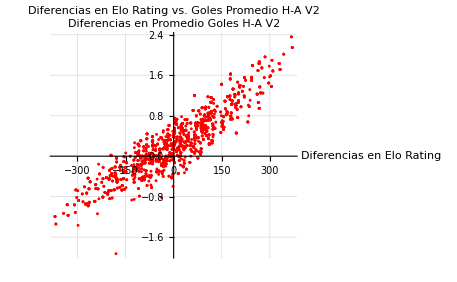

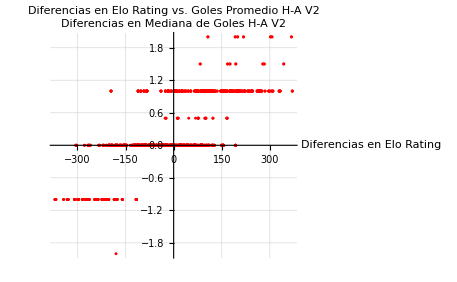

```mathematica
Show[
  ListPlot[Transpose[{dataDS[All,"DifferenceELO"]//Normal,dataDS[All,"DifferenceAverageGoalsHomeAway"]//Normal}], PlotStyle -> Red, 
   AxesLabel -> {"Diferencias en Elo Rating", "Diferencias en Promedio Goles H-A V2"}, 
   PlotLabel -> "Diferencias en Elo Rating vs. Goles Promedio H-A V2", 
   GridLines -> Automatic]
]

Show[
  ListPlot[Transpose[{dataDS[All,"DifferenceELO"]//Normal,dataDS[All,"DifferenceMedianGoalsHomeAway"]//Normal}], PlotStyle -> Red, 
   AxesLabel -> {"Diferencias en Elo Rating", "Diferencias en Mediana de Goles H-A V2"}, 
   PlotLabel -> "Diferencias en Elo Rating vs. Goles Promedio H-A V2", 
   GridLines -> Automatic]
]
```

```mathematica
Show[
  ListPlot[Transpose[{dataGroupByMatchMeanDS[All,"DifferenceELO"]//Normal, dataGroupByMatchMeanDS[All,"DifferenceGoals"]//Normal}], PlotStyle -> Red, 
   AxesLabel -> {"Diferencias en Elo Rating", "Diferencias en Promedio Ponderado Goles"}, 
   PlotLabel -> "Ajuste Lineal de Diferencias en Elo Rating vs. Goles Promedio", 
   GridLines -> Automatic]
]

Show[
  ListPlot[Transpose[{dataGroupByMatchMedianDS[All,"DifferenceELO"]//Normal, dataGroupByMatchMedianDS[All,"DifferenceGoals"]//Normal}], PlotStyle -> Red, 
   AxesLabel -> {"Diferencias en Elo Rating", "Diferencias en Promedio Ponderado Goles"}, 
   PlotLabel -> "Ajuste Lineal de Diferencias en Elo Rating vs. Goles Promedio", 
   GridLines -> Automatic]
]
```

### Explicacion ELO

initialElo
Description: The initial ELO rating assigned to every team before any matches are processed. It represents a baseline level from which teams can move up or down based on their performance.
Example Value: 1500

kFactor
Description: A constant that determines the magnitude of rating changes after each match. A higher K-factor results in larger changes, making the system more sensitive to individual match results.
Example Value: 30

expectedScore[ratingA_, ratingB_]
Description: A function that calculates the expected probability of a team (with a certain ELO rating) winning a match against another team (with a different ELO rating). The expected score is a value between 0 and 1.
Inputs:
ratingA_: The ELO rating of team A.
ratingB_: The ELO rating of team B.

updateElo[currentRating_, expected_, actual_]
Description: A function that updates a team’s ELO rating based on its current rating, the expected match outcome, and the actual match outcome.
Inputs:
currentRating_: The team’s current ELO rating.
expected_: The expected outcome calculated by expectedScore.
actual_: The actual outcome of the match (1 for a win, 0.5 for a draw, 0 for a loss).

eloRatings
Description: A dictionary (or association) that stores the ELO ratings for all teams. The keys are team names, and the values are their corresponding ELO ratings.
Example Value: <|”Liverpool” -> 1520, “Man City” -> 1480, ...|>

matches
Description: A list of match data where each match is represented as an association with details like the home team, away team, and goals scored by each team. This is a simplified representation of your actual match data.
Example Value:
wolfram
Copy code
{
  {“HomeTeam” -> “Liverpool”, “AwayTeam” -> “Man City”, “HomeGoals” -> 2, “AwayGoals” -> 1},
  {“HomeTeam” -> “Chelsea”, “AwayTeam” -> “Arsenal”, “HomeGoals” -> 0, “AwayGoals” -> 3},
  ...
}

homeTeam
Description: A variable that stores the name of the home team for the current match being processed.
Example Value: “Liverpool”

awayTeam
Description: A variable that stores the name of the away team for the current match being processed.
Example Value: “Man City”

homeGoals
Description: A variable that stores the number of goals scored by the home team in the current match.
Example Value: 2

awayGoals
Description: A variable that stores the number of goals scored by the away team in the current match.
Example Value: 1

homeRating
Description: The current ELO rating of the home team before the match result is applied.
Example Value: 1500

awayRating
Description: The current ELO rating of the away team before the match result is applied.
Example Value: 1500

homeExpected
Description: The expected score for the home team in the match, based on the current ELO ratings of both teams.
Example Value: 0.52

awayExpected
Description: The expected score for the away team in the match, based on the current ELO ratings of both teams.
Example Value: 0.48

homeActual
Description: The actual score for the home team in the match, determined by the match result. It can be 1 for a win, 0.5 for a draw, or 0 for a loss.
Example Value: 1

awayActual
Description: The actual score for the away team in the match, determined by the match result. It can be 1 for a win, 0.5 for a draw, or 0 for a loss.
Example Value: 0

finalEloRatings
Description: A list of the final ELO ratings for all teams, sorted in descending order. Each entry includes the team name and its final ELO rating.
Example Value:
wolfram
Copy code
{
  {“Liverpool”, 1765.69},
  {“Man City”, 1716.65},
  ...
}

Summary:
Initial Variables (initialElo, kFactor): Set up the starting conditions.
Functions (expectedScore, updateElo): Define the calculations for ELO ratings.
Match Processing Variables: Handle each match, update ratings, and store results.
Final Result (finalEloRatings): Present the sorted ELO ratings of the teams after processing all matches.